```mathematica
Limit[(Sin[x]/x),x->0]
```

1

```mathematica
Limit[(x^3-4x-15)/(x-3),x->3]
```

23

```mathematica
Limit[(x^3-5x)/(2*x^3-3*x^2),x->∞]
```

1/2

```mathematica
D[x^x,{x,1}]
```

x^x (1+Log[x])

```mathematica
D[%,{x,1}]
```

x^(-1+x)+x^x (1+Log[x])^2

```mathematica
D[x^x,{x,3}]
```

2 x^(-1+x) (1+Log[x])+x^x (1+Log[x])^3+x^(-1+x) ((-1+x)/x+Log[x])

```mathematica
D[5x^5+4x^4+9x^3-16^2+7x+2,{x,1}]
```

7+27 x^2+16 x^3+25 x^4

```mathematica
D[%,{x,1}]
```

54 x+48 x^2+100 x^3

```mathematica
D[%,{x,1}]
```

54+96 x+300 x^2

```mathematica
D[Sin[x*y],{y,3},{x,2}]
```

-6 x Cos[x y]+x^3 y^2 Cos[x y]+6 x^2 y Sin[x y]

```mathematica
D[Sin[x*y],{x,2},{y,3}]
```

-6 x Cos[x y]+x^3 y^2 Cos[x y]+6 x^2 y Sin[x y]

```mathematica
Integrate[Sin[a*x+b],x]
```

-(Cos[b] Cos[a x])/a+(Sin[b] Sin[a x])/a

```mathematica
Integrate[(Log[x])^3,x]
```

-6 x+6 x Log[x]-3 x Log[x]^2+x Log[x]^3

```mathematica
Integrate[(E^-x),{x,0,a}]
```

1-ⅇ^-a

```mathematica
Integrate[Sin[x],{x,0,Pi/2}]
```

1

```mathematica
Series[Log[x],{x,Pi/2,8}]
```

Log[π/2]+(2 (x-π/2))/π-(2 (x-π/2)^2)/π^2+(8 (x-π/2)^3)/(3 π^3)-(4 (x-π/2)^4)/π^4+(32 (x-π/2)^5)/(5 π^5)-(32 (x-π/2)^6)/(3 π^6)+(128 (x-π/2)^7)/(7 π^7)-(32 (x-π/2)^8)/π^8+O[x-π/2]^9

```mathematica
Series[Sin[x],{x,Pi/2,8}]
```

1-1/2 (x-π/2)^2+1/24 (x-π/2)^4-1/720 (x-π/2)^6+(x-π/2)^8/40320+O[x-π/2]^9

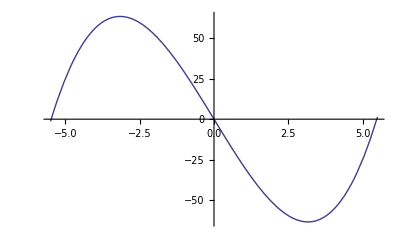

```mathematica
Plot[x^3-30x,{x,-5.5,5.5}]
```

```mathematica
FindMaximum[x^3-30x,{x,-5}]
```

{63.2456,{x→-3.16228}}

```mathematica
FindMaximum[x^3-30x,{x,-5}]
```

{63.2456,{x→-3.16228}}

```mathematica
FindMinimum[x^3-30x,{x,5}]
```

{-63.2456,{x→3.16228}}